```mathematica
ClearAll["Global`*"]
```

```mathematica
π:= 3.141592653589793;
```

SetDelayed::wrsym: Symbol π is Protected.

```mathematica
FmToNu :=0.00506773123;
gamma :=0.5772;
mp = 938.2;
mpion = 139.570;
md = 1875.61;
a0 = 52917.724900001;
```

```mathematica
chargeRag[m1_,m2_,charge_]:= a0* 0.510/(m1*m2/(m1+m2)*charge);
```

```mathematica
chargeRag[mpion,md,-1]
chargeRag[139.570,139.570,1]
```

-207.755

386.731

```mathematica
Ac[η_]:= 2.0*π*η*1.0/(Exp[2.0*π*η]-1);
```

```mathematica
(* trucketed series is not good h[η_]:=If[Abs[η]<0.3,(1.2 η^2 -Log[Abs[η]]-gamma),(η^2*Sum[1/(n(n^2+η^2)),{n,1,100000}]-gamma -Log[Abs[η]]) ];*)
```

```mathematica
h[η_]:=If[Abs[η]<0.3,(1.2 η^2 -Log[Abs[η]]-gamma),(η^2*Sum[1/(n(n^2+η^2)),{n,1,100000}]-gamma -Log[Abs[η]]) ];
```

```mathematica
fc[k_,f0_,d0_,ac_,η_]:=1.0/(1/f0+1/2*d0* k*k-2.0/ac*h[η]-ⅈ * k*Ac[η]);
```

```mathematica
TildeG[ρ_,η_]:=Sqrt[Ac[η]]*(ⅈ *CoulombF[0,η,ρ]+CoulombG[0,η,ρ])
```

```mathematica
F[η_,ζ_]:=Hypergeometric1F1[ⅈ η,1,ⅈ ζ];
```

```mathematica
ψ[k_,r_,t_,ScatLen_,EffecRange_,ChargeRad_]:=Module[{η,ρ,f0,d0,ac,ζ,rval,WF},
η:=1.0/(k*ChargeRad)/FmToNu;
ρ:=k*r*FmToNu;
ζ:=ρ*(1+t);
f0:=ScatLen*FmToNu;
d0:=EffecRange*FmToNu;
ac:=ChargeRad*FmToNu;
rval:=r*FmToNu;
WF:=Power[Ac[η],0.5]*Exp[ⅈ*Arg[Gamma[1+ⅈ*η]]]*(Exp[-ⅈ*k*rval*t]*F[-η,ζ]+fc[k,f0,d0,ac,η]*TildeG[ρ,η]/rval);
N[WF]
]
```

```mathematica
(*Elastice and inelastic part*)
```

Export data for pd in text file

```mathematica
dCky[k_,ScatLen_,EffecRange_,ChargeRad_,rval_]:=Module[{Ck },
Ck:=NIntegrate[(Abs[Conjugate[ψ[k,rval,t,ScatLen,EffecRange,ChargeRad]]*ψ[k,rval,t,ScatLen,EffecRange,ChargeRad]])rval*rval*FmToNu*FmToNu*FmToNu*2.0*π,{t,-1.0,1.0}];
N[Ck]
]
```

```mathematica
(*totaldCky[k_,r_]:=1/3*Quiet[dCky[k,-0.0240,2.27,43.15,r]]+2.0/3.0*Quiet[dCky[k,-13.7,2.63,43.15,r]]*)
```

```mathematica
totaldCky[k_,r_]:=Quiet[dCky[k,0.037-ⅈ*0.008,0,-207.7545607992,r]]
```

```mathematica
exportFile[k_]:=Module[{ckfileName,OutputFolder},
OutputFolder:="/home/sbhawani/Desktop/Wioleta/PiminusD/";
ckfileName = ToString[StringForm[OutputFolder<>"Cky_k"<>"``"<>".dat",k ]];
CkTabledCkpd=Table[{NumberForm[r,4],totaldCky[k,r]},{r,0.001,80.0,0.2}];
Export[ckfileName,CkTabledCkpd,"Table"];
]
```

```mathematica
(*I would run this part only if i need to generate new dCk_y files. For now you have dCk_y files from me but in future if you would like to have another CF for different sets of scattering parameters you may try this:)*)
```

```mathematica
(*For[i = 1,i<=80,i++,exportFile[i*5]]*)
```

```mathematica
Source[r_,R_]:=Module[{Sr,Rad,rad},
Rad:=R*FmToNu;
rad:=r*FmToNu;
Sr := 1/(4 *π Rad^2)^(3/2)*Exp[-rad^2/4/Rad^2];
Sr
]
```

```mathematica
GETCORRELATION[k_,ScatLen_,EffecRange_,ChargeRad_,SourceRad_]:=Module[{Ck },
Ck:=NIntegrate[(Abs[Conjugate[ψ[k,r,t,ScatLen,EffecRange,ChargeRad]]*ψ[k,r,t,ScatLen,EffecRange,ChargeRad]])*Source[r,SourceRad]*r*r*FmToNu*FmToNu*FmToNu*2.0*π,{t,-1.0,1.0},{r,0.0,80.0}];
N[Ck]
]
```

```mathematica
GETCORRELATION[10,0.037-ⅈ*0.008,0.0,-207.7545607992,1.0]
```

1.3583

```mathematica
mk = 493.67
```

493.67

```mathematica
chargeRag[mk,md,1]
```

69.0571

```mathematica
(* YOU SHOULD UNCOMMENT IT IF YOU WANT TO GET DIRECTLY CF(k)FROM THE MATHEMATICA NOTEBOOK CkTable1 =Table[{k,Quiet[GETCORRELATION[k,0.037-ⅈ*0.008,0.0,-207.7545607992,10.0]]},{k,5,300,5}];*)
```

```mathematica
(*Export["/home/sbhawani/Desktop/Wioleta/PiminusD/PiMinusD10p0.dat",CkTable1,"Table"];*)
```

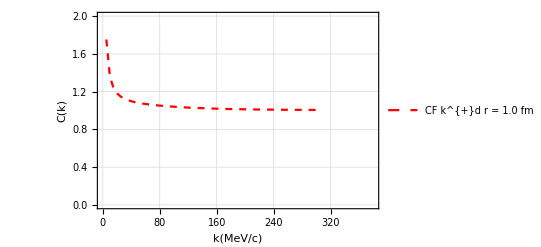

```mathematica
(* this is what i sent as C(k) for radius 1 fm, PlotCkKdD1=ListPlot[CkTable1,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,380},{0,
2.}},BaseStyle->{FontSize,16},PlotLegends->{"CF k^{+}d r = 1.0 fm"},PlotStyle->{Red,Dashed}]*)
```

```mathematica
(*OutputFolderOfCkKplusD:="/home/sbhawani/Desktop/kplusD/CkKplusDRad1p0.dat";
Export[OutputFolderOfCkKplusD,CkTable1,"Table"];*)
```

```mathematica
source[r_,rR_]:=With[
{rRad=rR*FmToNu,rad=r*FmToNu},
 (1/(4 π rRad^2))^(3/2)*Exp[-rad^2/(4 rRad^2)]
]
```

```mathematica
SourceTable =Table[{r,source[r,8.059]*4*3.14*r*r},{r,0,50,0.01}];
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Visualization`Utilities`ScaleCatPlotRange[ListPlot,#1,#2]&,{{{0,50}},{{Identity,Identity},{Identity,Identity}}}]; dimensions are 1 and 2.

ListPlot::prng: Value of option PlotRange -> MapThread[Visualization`Utilities`ScaleCatPlotRange[ListPlot,#1,#2]&,{{{0,50}},{{Identity,Identity},{Identity,Identity}}}] is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

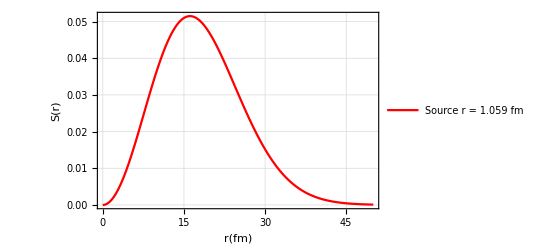

```mathematica
PlotSource=ListPlot[SourceTable,Frame->True,FrameLabel->{"r(fm)","S(r)"},Joined->True,GridLines->Automatic,PlotRange->{{0,50}},BaseStyle->{FontSize,16},PlotLegends->{"Source r = 1.059 fm"},PlotStyle->Red]
```

```mathematica
(*here this part the codes run and scan read the dCky files that I send you, it does with interpolation*)
```

```mathematica
getdCk2[k_]:=Module[{filename},
filename :=ToString[StringForm["/home/sbhawani/Desktop/Wioleta/PiminusD/Cky_k``.dat",k ]] ;
Interpolation[{#[[1]],#[[2]]}&/@Import[filename,"Table",HeaderLines->1]]
]
dCk:=getdCk2[10]
dCk[10.0]
```

0.000199355

```mathematica
(*finally you can inetegrate it and get the correlation, this is also done is the macro C# which i sent you in the previous email however there i didn't do any interpolation, results are same because the steps in r* are very small *)
```

```mathematica
GETCORRELATIONPION[k_,SourceRad_]:=Module[{Ck ,dCk=getdCk2[k]},
Ck:=NIntegrate[dCk[r]*source[r,SourceRad],{r,0.001,30.00}];
N[Ck]
]
```

```mathematica
GETCORRELATIONPION[5,1.0]
```

1.75247

```mathematica
CkTable11 =Table[{k,Quiet[GETCORRELATIONPION[k,1.0]]},{k,5,400,5}];
```

```mathematica
CkTable2 =Table[{k,Quiet[GETCORRELATION[k,1.5]]},{k,5,400,5}];
```

```mathematica
CkTable3 =Table[{k,Quiet[GETCORRELATION[k,2.0]]},{k,5,400,5}];
```

```mathematica
CkTable4 =Table[{k,Quiet[GETCORRELATION[k,3.0]]},{k,5,400,5}];
```

```mathematica
CkTable5 =Table[{k,Quiet[GETCORRELATION[k,4.0]]},{k,5,400,5}];
```

```mathematica
CkTable6 =Table[{k,Quiet[GETCORRELATION[k,5.0]]},{k,5,400,5}];
```

```mathematica
CkTable7 =Table[{k,Quiet[GETCORRELATION[k,14.0]]},{k,5,400,5}];
```

```mathematica
PlotCkPdD1=ListPlot[CkTable11,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,400},{0,
2}},BaseStyle->{FontSize,16},PlotLegends->{"CF kd r = 1.0"},PlotStyle->Red];
```

```mathematica
PlotCkPdD2=ListPlot[CkTable2,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,400},{0,
20}},BaseStyle->{FontSize,16},PlotLegends->{"CF kd r = 1.5"},PlotStyle->Green];
```

```mathematica
PlotCkPdD3=ListPlot[CkTable3,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,400},{0,
20}},BaseStyle->{FontSize,16},PlotLegends->{"CF kd r = 2.0"},PlotStyle->Black];
```

```mathematica
PlotCkPdD4=ListPlot[CkTable4,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,400},{0,
20}},BaseStyle->{FontSize,16},PlotLegends->{"CF kd r = 3.0"},PlotStyle->Yellow];
```

```mathematica
PlotCkPdD5=ListPlot[CkTable5,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,400},{0,
20}},BaseStyle->{FontSize,16},PlotLegends->{"CF kd r = 4.0"},PlotStyle->Blue];
```

```mathematica
PlotCkPdD6=ListPlot[CkTable6,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,400},{0,
20}},BaseStyle->{FontSize,16},PlotLegends->{"CF kd r = 5.0"},PlotStyle->Orange];
```

```mathematica
PlotCkPdD7=ListPlot[CkTable7,Frame->True,FrameLabel->{"k(MeV/c)","C(k)"},Joined->True,GridLines->Automatic,PlotRange->{{0,400},{0,
20}},BaseStyle->{FontSize,16},PlotLegends->{"CF kd r = 8.0"},PlotStyle->Gray];
```

```mathematica
Show[
PlotCkPdD1,PlotCkPdD2 ,PlotCkPdD3,PlotCkPdD4,PlotCkPdD5,PlotCkPdD6,PlotCkPdD7,
PlotRange->{{0,400},{0.9,1.9}},
FrameLabel->{"k(MeV/c)","C(k)"}]
```

Show::gcomb: Could not combine the graphics objects in Show[PlotCkPdD1,PlotCkPdD2,PlotCkPdD3,PlotCkPdD4,PlotCkPdD5,PlotCkPdD6,PlotCkPdD7,PlotRange→{{0,400},{0.9,1.9}},FrameLabel→{k(MeV/c),C(k)}].

Show[PlotCkPdD1,PlotCkPdD2,PlotCkPdD3,PlotCkPdD4,PlotCkPdD5,PlotCkPdD6,PlotCkPdD7,PlotRange→{{0,400},{0.9,1.9}},FrameLabel→{k(MeV/c),C(k)}]